```mathematica
<<GroupMath`
```

paclet:GroupMath/tutorial/GroupMathDoc | XXXXXXXXXXXXXXXXXXXXXXXXXXX GroupMath XXXXXXXXXXXXXXXXXXXXXXXXXXVersion: 1.1.2 (6/May/2020)Author: Renato FonsecaReference: 2011.01764 [hep-th]Website: http://renatofonseca.net/groupmathBuilt-in documentation: paclet:GroupMath/tutorial/GroupMathDocXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXX

SetDelayed::write: Tag BlockDiagonalMatrix in BlockDiagonalMatrix[blocks_] is Protected.

```mathematica
(*Primitive for drawing wBa Bratteli diagram*)
BratteliLevels[p_,q_,d_]:=Table[{x,{},i},{i,0,p},{x,IntegerPartitions[i,d]}]~Join~Table[Flatten[Table[{x,y,p+i},{k,0,Min[p,i]},{x,IntegerPartitions[p-k,d]},{y,IntegerPartitions[i-k,d-Length@x]}],2],{i,1,q}]
Contains[x_,y_]:=Module[{d,xn,yn},
d=Max[Length[x],Length[y]];
{xn,yn}={PadRight[x,d],PadRight[y,d]};
AllTrue[{xn,yn}ᵀ,#[[1]]>=#[[2]]&]
]
OrderWBA[x_,y_]:=If[x[[3]]+1==y[[3]],
If[(Total[x[[1]]]==x[[3]])&&(Total[y[[1]]]==y[[3]]),
Contains[y[[1]],x[[1]]],
If[(Total[x[[1]]]<=x[[3]])&&(Total[y[[1]]]<y[[3]]),
If[Total[y[[1]]]==Total[x[[1]]],
Contains[y[[2]],x[[2]]]&&Contains[x[[1]],y[[1]]],
If[Total[y[[2]]]==Total[x[[2]]],
Contains[x[[2]],y[[2]]]&&Contains[x[[1]],y[[1]]],
False],False]],False],False]
```

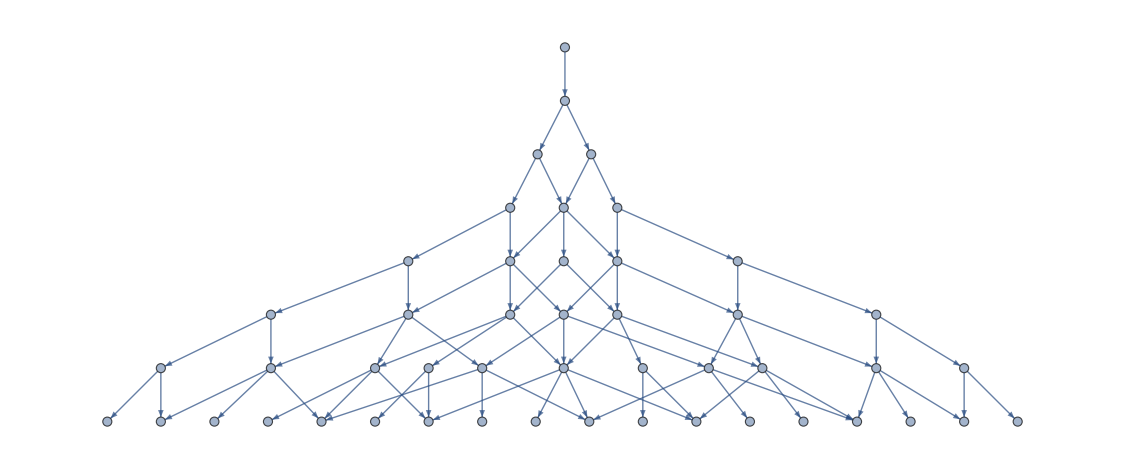

```mathematica
{p,q,d}={6,1,7};
g=RelationGraph[OrderWBA,Flatten[BratteliLevels[p,q,d],1],GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
(*GraphicsGrid[Table[Null,{i,λ[[1,1]]},{j,λ[[1,1]]}],Frame->Join[{None},{None},{Flatten[With[{cc=(Range@#&)/@λ[[1]]},Table[Flatten[{nn,#}->True&/@cc[[nn]],1],{nn,Length@cc}]],1]}],ImageSize->10]*)
```

```mathematica
EdgeList[g]
```

{{{},{},0}->{{1},{},1},{{1},{},1}->{{2},{},2},{{1},{},1}->{{1,1},{},2},{{2},{},2}->{{3},{},3},{{2},{},2}->{{2,1},{},3},{{1,1},{},2}->{{2,1},{},3},{{3},{},3}->{{3},{1},4},{{3},{},3}->{{2},{},4},{{2,1},{},3}->{{2},{},4},{{2,1},{},3}->{{1,1},{},4},{{3},{1},4}->{{3},{2},5},{{3},{1},4}->{{2},{1},5},{{2},{},4}->{{2},{1},5},{{2},{},4}->{{1},{},5},{{1,1},{},4}->{{1},{},5}}

```mathematica
(*VertexLabels->((#->{#[[1]],#[[2]]})&/@VertexList[g])*)
VertexList[g]
```

{{{},{},0},{{1},{},1},{{2},{},2},{{1,1},{},2},{{3},{},3},{{2,1},{},3},{{3},{1},4},{{2},{},4},{{1,1},{},4},{{3},{2},5},{{2},{1},5},{{1},{},5}}

```mathematica
newVs=Table[Annotation[λ,VertexShape->Text[λ[[1;;2]]]],{λ,VertexList[g]}];
Graph[newVs,EdgeList[g],VertexSize->0.4,GraphLayout->"LayeredDigraphEmbedding"];
```

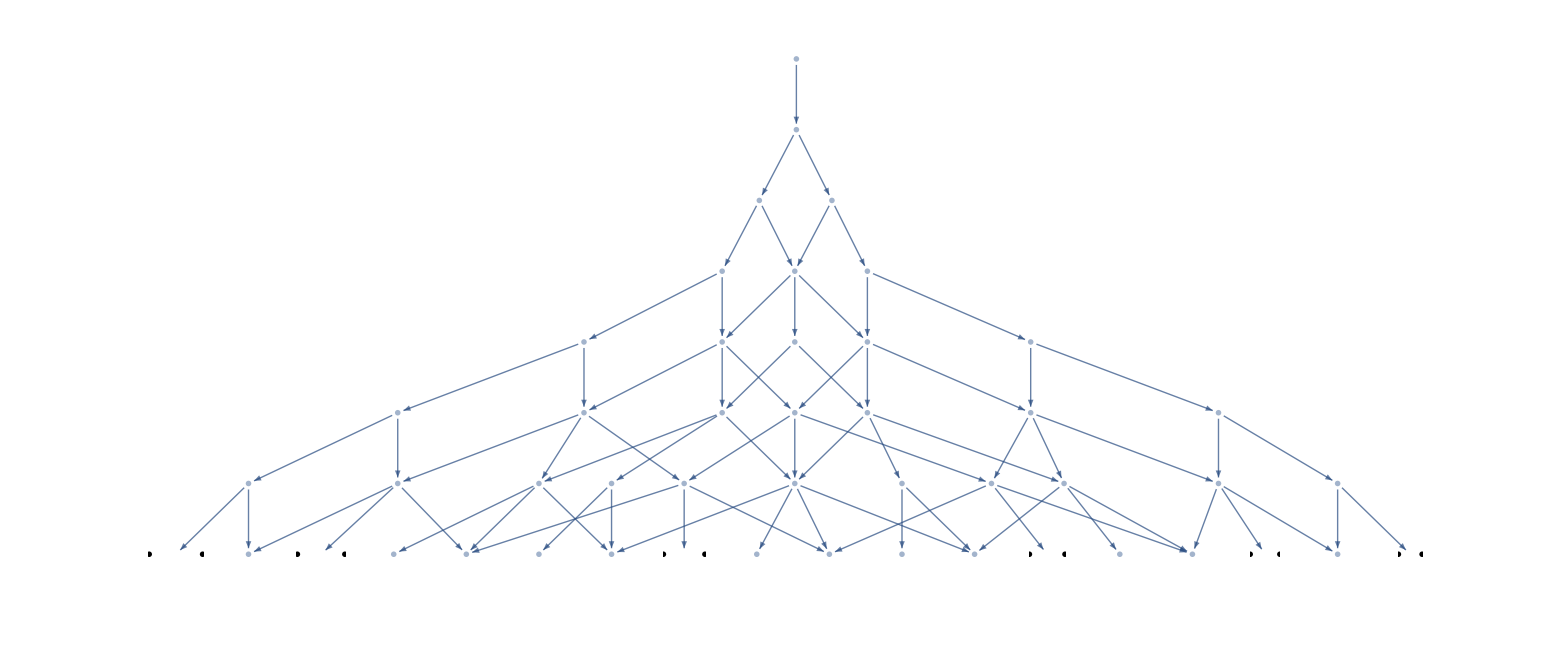

```mathematica
newVs=Table[Annotation[λ,VertexShape->GraphicsGrid[{{If[λ[[1]]=={},Text[∅],YoungDiagram[λ[[1]]]],If[λ[[2]]=={},Text[∅],YoungDiagram[λ[[2]]]]}}]],{λ,VertexList[g]}];
sizes=Table[λ->Max[If[λ[[1]]=={},1,λ[[1,1]]],If[λ[[2]]=={},1,λ[[2,1]]]]*0.1+0.3,{λ,VertexList[g]}];
Graph[newVs,EdgeList[g],VertexSize->sizes,GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
{YoungDiagram[#[[1]]],YoungDiagram[#[[2]]]}&/@{{{},{}},{{1},{}},{{2},{}},{{3},{}},{{3},{1}},{{2},{1}}}
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}